```mathematica
PressureMatrix[coefficients_,source_,nObjects_,resolution_,verbose_:False]:=Module[{n,r,E,V,M, v},
n=resolution; r = nObjects;
E=coefficients[n];
V=source[n];
M=IdentityMatrix[r n] + (Table[Table[E[α,β][i,j],{i,1,n},{j,1,n}],{α,1,r},{β,1,r}]//ArrayFlatten//N);
v=ParallelTable[Table[V[α,β][i,j],{i,1,n},{j,1,n}],{α,1,r},{β,1,r}]//ArrayFlatten//N;

If[verbose,
Print[{ListPlot3D[M],ListPlot3D[M,PlotRange->{0,All}],ListPlot3D[M,PlotRange->{All,0}]}];
Print[ListPlot3D[v,PlotRange->{All,0}]]
];

LinearSolve[M,v]
];

PressureVector[coefficients_,source_,nObjects_,resolution_]:=Module[{n,r,m,E,V,M,v},
n=resolution;r=nObjects;
m=Floor[n/2];
E=coefficients[n];
V=source[n];

M=IdentityMatrix[r n] + (Table[Table[E[α,β][i,j],{i,1,n},{j,1,n}],{α,1,r},{β,1,r}]//ArrayFlatten//N);
v=ParallelTable[V[α,1][i,m],{α,1,r},{i,1,n}]//Flatten//N;
LinearSolve[M,v]
];

PressurePoint[coefficients_,source_,nObjects_,resolution_]:=
PressureVector[coefficients, source, nObjects, resolution][[resolution/2]]


CasimirPressure[coefficients_, source_, nObjects_, resolution_]:=Module[{P},
P = PressureMatrix[coefficients, source, nObjects, resolution];
Table[P[[k,k]],{k,1,resolution}]
];

Force[coefficients_, source_, nObjects_, resolution_]:=Module[{integrand,wmax,dw,pts},
integrand[w_]:=If[w==0,0,w^2 PressurePoint[coefficients[w],source[w],nObjects,resolution]];
wmax=6;
dw=wmax/30;
pts=Monitor[Table[integrand[w],{w,0,wmax,dw}],ProgressIndicator[w,{0,wmax}]];
ListLinePlot[pts//WithXRegion[0,wmax]]//Print;
SimpsonSum[dw, pts]
];
```

```mathematica
(* UNIT TESTS *)
Module[{testVectorMatchesMatrix,testPointMatchesVector},
testVectorMatchesMatrix[]:=Module[{c,s,P,p},
c=plateCoefficients[1,10][1];
s=plateSource[1,10][1];
P=PressureMatrix[c,s,2,15];
p=PressureVector[c,s,2,15];
AllTrue[p==Table[P[[15,k]],{k,1,30}],TrueQ]
];
testPointMatchesVector[]:=Module[{c,s,P,p},
c=plateCoefficients[1,10][1];
s=plateSource[1,10][1];
P=PressureVector[c,s,2,20];
p=PressurePoint[c,s,2,20];
TrueQ[p==P[[10]]]
];

AssertTrue[testVectorMatchesMatrix[]] //Print;
AssertTrue[testPointMatchesVector[]]//Print;
];
```

True

True

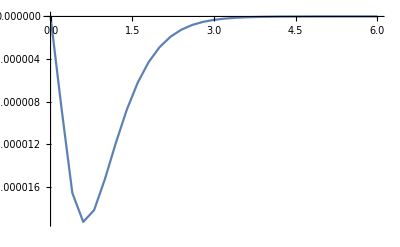

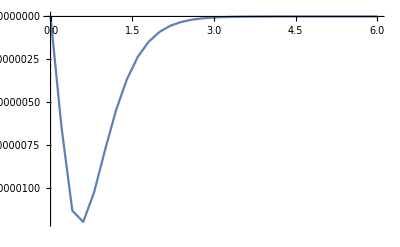

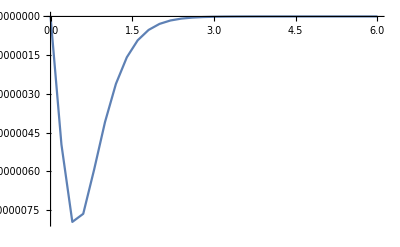

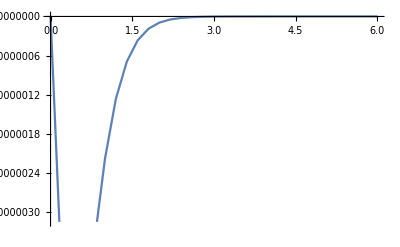

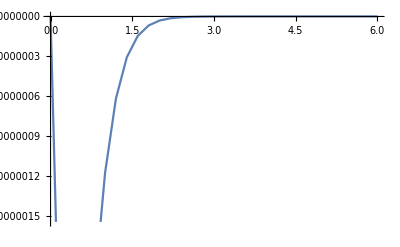

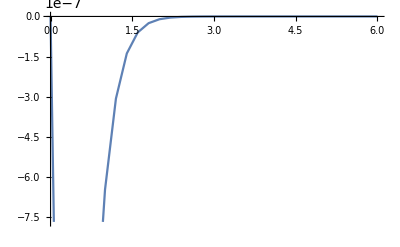

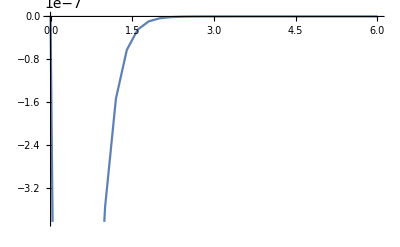

{-0.0000235026,-0.0000126868,-7.44334×10^-6,-4.65433×10^-6,-3.06057×10^-6,-2.09621×10^-6,-1.48476×10^-6}

```mathematica
pts=Table[
Force[plateCoefficients[a,0.01],plateSource[a,0.01], 2, 20],
{a,{1.5,1.75,2,2.25,2.5,2.75,3}}
]
```

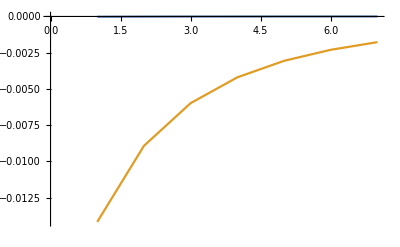

```mathematica
ListLinePlot[{pts,Table[plateExact[a],{a,{1.5,1.75,2,2.25,2.5,2.75,3}}]}]
```